9331

1

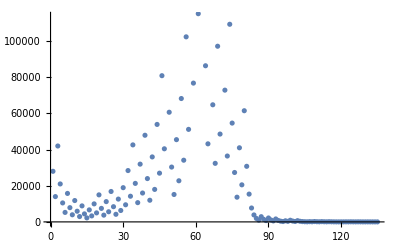

```mathematica
(* question 1 a*)
n1=n=RandomInteger[{1000,9999}]
set={};
While[n1≠1,If[EvenQ[n1],n1=n1/2,n1=n1*3+1];set=Append[set,n1]]
n1

ListPlot[set]
```

```mathematica
(*Question 1 b*)
Select[Range[1000],PerfectNumberQ]
```

{6,28,496}

```mathematica
(*Question 2*)
T[{x_,y_,z_}]={3 x-z,x+y+2 z,x-y+3 z};
T[1,5,0]+T[3,1,8]
```

{4,26,22}

```mathematica
a=RowReduce[({{3, 0, -1, 0}, {1, 1, 2, 0}, {1, -1, 3, 0}})]
MatrixRank[a]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0}}

3

```mathematica
(*Dimension of ker[T] is 0, basis is {}*)
RowReduce[{T[1,0,0],T[0,1,0],T[0,0,1]}]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(* Dimension of Im[T] is 3, basis is {e1,e2,e3}*)
Clear[a];
s=Solve[T[x,y,z]=={a,b,c},{x,y,z}]
```

{{x→1/17 (5 a+b+c),y→1/17 (-a+10 b-7 c),z→1/17 (-2 a+3 b+3 c)}}

```mathematica
t[{a_,b_,c_}]={s[[1,1,2]],s[[1,2,2]],s[[1,3,2]]};
t[x,y,z]
T[t[{x,y,z}]]//Expand
```

{1/17 (5 x+y+z),1/17 (-x+10 y-7 z),1/17 (-2 x+3 y+3 z)}

{x,y,z}

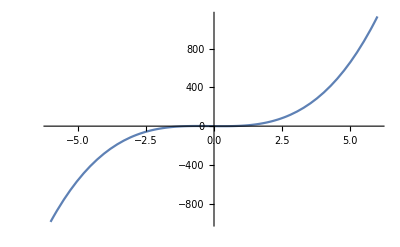

{1.44,{x→-0.6}}

{-0.592593,{x→0.333333}}

```mathematica
f[x_]=5 x^3+2 x^2-3x;
Plot[f[x],{x,-6,6}]
FindMaximum[f[x],{x,0}]
FindMinimum[f[x],{x,5}]
```

```mathematica
(*Question n0 4 a*)
∑_(i=1)^∞ (i+2)/(i*(i+1))
```

Sum::div: Sum does not converge.

```mathematica
∑_(i=1)^5 (2+i)/(i (1+i))
```

187/60

```mathematica
c=1+I/(1-1/(1+1/I));
Arg[c]
Abs[c]
```

π/2

1

```mathematica
I^2
```

-1

```mathematica
A=({{x, y, z, 1}, {1, 0, 0, 1}, {0, -3, 0, 1}, {0, 0, 4, 1}});
Det[A]
```

12-12 x+4 y-3 z